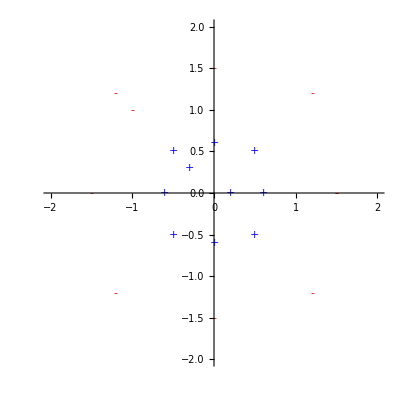

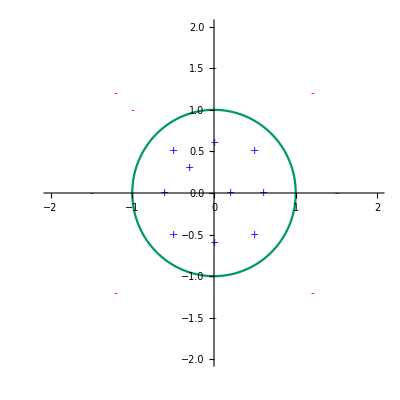

Φ[{u_1,u_2}] = {1,u_1,u_2,u_1^2,u_2^2,u_1 u_2}

K[u^-,v^-] = K[{u_1,u_2}, {v_1,v_2}] = Φ[u^-].Φ[v^-]= Φ[{u_1,u_2}] . Φ[{v_1,v_2}] = 1+u_1 v_1+u_1^2 v_1^2+u_2 v_2+u_1 u_2 v_1 v_2+u_2^2 v_2^2

(1 | {-0.3,0.3} | 1
2 | {0.6,0.} | 1
3 | {-1.2,1.2} | -1
4 | {-1.2,-1.2} | -1
5 | {0.,-1.5} | -1
6 | {1.5,0.} | -1
7 | {0.5,-0.5} | 1
8 | {1.2,1.2} | -1
9 | {1.2,-1.2} | -1
10 | {1.5,0.} | -1
11 | {0.5,0.5} | 1
12 | {-0.6,0.} | 1
13 | {0.2,0.} | 1
14 | {-0.5,0.5} | 1
15 | {0.,1.5} | -1
16 | {-1.5,0.} | -1
17 | {-0.5,-0.5} | 1
18 | {0.,0.6} | 1
19 | {-1.,1.} | -1
20 | {0.,-0.6} | 1) → (1 | {1,-0.3,0.3,0.09,0.09,-0.09} | 1
2 | {1,0.6,0.,0.36,0.,0.} | 1
3 | {1,-1.2,1.2,1.44,1.44,-1.44} | -1
4 | {1,-1.2,-1.2,1.44,1.44,1.44} | -1
5 | {1,0.,-1.5,0.,2.25,0.} | -1
6 | {1,1.5,0.,2.25,0.,0.} | -1
7 | {1,0.5,-0.5,0.25,0.25,-0.25} | 1
8 | {1,1.2,1.2,1.44,1.44,1.44} | -1
9 | {1,1.2,-1.2,1.44,1.44,-1.44} | -1
10 | {1,1.5,0.,2.25,0.,0.} | -1
11 | {1,0.5,0.5,0.25,0.25,0.25} | 1
12 | {1,-0.6,0.,0.36,0.,0.} | 1
13 | {1,0.2,0.,0.04,0.,0.} | 1
14 | {1,-0.5,0.5,0.25,0.25,-0.25} | 1
15 | {1,0.,1.5,0.,2.25,0.} | -1
16 | {1,-1.5,0.,2.25,0.,0.} | -1
17 | {1,-0.5,-0.5,0.25,0.25,0.25} | 1
18 | {1,0.,0.6,0.,0.36,0.} | 1
19 | {1,-1.,1.,1.,1.,-1.} | -1
20 | {1,0.,-0.6,0.,0.36,0.} | 1)

```mathematica
ClearAll[f,x,k];

numin = 10;
numout = 20;

(* initialize data *)
posPts={{0.2,0.0},{0.5,0.5},{0.5,-0.5},{-0.5,0.5},{-0.5,-0.5},{0.0,0.6},{0.6,0.0},{-0.6,0.0},{0.0,-0.6},{-0.3,0.3}};
negPts={{1.5,0.0},{1.2,1.2},{1.2,-1.2},{-1.2,1.2},{-1.2,-1.2},{0.0,1.5},{1.5,0.0},{-1.5,0.0},{0.0,-1.5},{-1.0,1.0}};
allPts = {posPts, negPts};

picpts = Show[{
 ParametricPlot[{0,0}
,{t,0,2}
,PlotStyle->RGBColor[0,0.6,0.4]
,PlotRange->{{-2,2},{-2,2}}]
,
Graphics[{
   Blue,Map[Text[Style["+",Large],#]&,posPts]
,Red,Map[Text[Style["-",Large],#]&,negPts]
}]
}];

Print[picpts];

(*parametric plot*)
Print[Show[{
 ParametricPlot[{Cos[t],Sin[t]}
,{t,0,2π}
,PlotStyle->RGBColor[0,0.6,0.4]
,PlotRange->{{-2,2},{-2,2}}]
,
picpts
}]
];


Φ[{x_,y_}] := {1,x,y,x^2,y^2,x y};
k[u_,v_] := Φ[u].Φ[v];

Print["Φ[",{"u_1","u_2"},"] = ",Φ[{"u_1","u_2"}]];
Print["K[u^-,v^-] = K[",{"u_1","u_2"},", ",{"v_1","v_2"},"] = Φ[u^-].Φ[v^-]= Φ[",{"u_1","u_2"},"] . Φ[",{"v_1","v_2"},"] = ",k[{"u_1","u_2"},{"v_1","v_2"}]];

newPosPts = Map[Φ,posPts];
newNegPts = Map[Φ,negPts];

Do[
posPts[[i]] = {i,posPts[[i]],1};
,{i,1,Length[posPts]}];
Do[
negPts[[i]] = {i,negPts[[i]],-1};
,{i,1,Length[negPts]}];

data = RandomSample[Flatten[{posPts,negPts},1]];
data = Transpose[data];
data[[1]] = Table[i,{i,1,Length[data[[1]]]}];

Φdata = data;
Φdata[[2]] = Map[Φ,data[[2]] ];
data = Transpose[data];
Φdata = Transpose[Φdata];

Print[MatrixForm[data]," → ",MatrixForm[ Φdata] ];

{ids,xs,ys} = Transpose[data];
len = Length[ids];
```

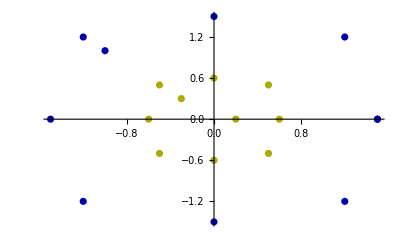

```mathematica
ListPlot[allPts,PlotStyle->Darker@{Yellow,Blue,Green}]
```

```mathematica
c=Classify[<|Yellow->allPts[[1]],Blue->allPts[[2]]|>,Method->"SupportVectorMachine"]
```

ClassifierFunction[…]

-Graphics3D-

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

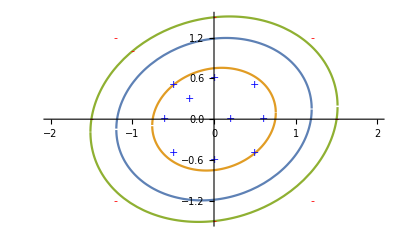

```mathematica
(*3D plot that visualizes the probability decision boundary between two classes (Has Diabetes and Does not have Diabetes) using a classifier function c.The plot shows the 3D surface for each class probability and overlays the original data points (allPts) colored by their respective class.*)
Show[Plot3D[{c[{x,y},"Probability"->Yellow],c[{x,y},"Probability"->Blue]},{x,-4,4},{y,-5,4},Exclusions->None],ListPointPlot3D[Map[Append[#,1]&,allPts,{2}],PlotStyle->{Yellow,Blue}]]
```

```mathematica
ClearAll[findαbKernelNoSlack,findαbKernelWithSlack,f,linearClass];

findαbKernelNoSlack[xs_,ys_] := Module[{len,αs,α,lag,constraints,maxval,αNum,αsVals,w,b,ele},  (* No slack variables *)

len = Length[xs];
αs = Table[α[i] ,{i,1,len}];
lag = Simplify[Plus@@Table[α[i] ,{i,1,len}]-1/2 Plus@@Flatten[Table[α[i] α[j] ys[[i]] ys[[j]] k[xs[[i]],xs[[j]]] ,{i,1,len},{j,1,len}]]];
constraints = Table[α[i] ≥  0 ,{i,0,len}];
constraints[[1]]= Plus@@Table[α[i] ys[[i]] ,{i,1,len}]==0;


{maxval,αNum} = NMaximize[{lag,constraints},αs ];                   (* this is an important line of code! *)


αsVals = αs/.αNum;

ele = FirstPosition[αsVals,Max[αsVals]][[1]];
b = ys[[ele]]-Plus@@Table[αsVals[[i]] ys[[i]]  k[xs[[i]],xs[[ele]]] ,{i,1,len}];

Return[{ys*αsVals,b}];
];


findαbKernelWithSlack[xs_,ys_,c_] := Module[{len,αs,α,lag,constraints,maxval,αNum,αsVals,w,b,ele},  (* No slack variables *)

len = Length[xs];
αs = Table[α[i] ,{i,1,len}];
lag = Simplify[Plus@@Table[α[i] ,{i,1,len}]-1/2 Plus@@Flatten[Table[α[i] α[j] ys[[i]] ys[[j]] k[xs[[i]],xs[[j]]] ,{i,1,len},{j,1,len}]]];
constraints = Table[   c ≥ α[i] ≥  0 ,{i,0,len}];
constraints[[1]]= Plus@@Table[α[i] ys[[i]] ,{i,1,len}]==0;


{maxval,αNum} = NMaximize[{lag,constraints},αs ];                   (* this is an important line of code! *)


αsVals = αs/.αNum;

ele = FirstPosition[αsVals,Max[Map[If[(#<0.0001)|| #>0.999 c,0,#]&, αsVals]]][[1]];  (*  max(αsVals) thats not c *)
b = ys[[ele]]-Plus@@Table[αsVals[[i]] ys[[i]]  k[xs[[i]],xs[[ele]]] ,{i,1,len}];

Return[{ys*αsVals,b}];
];

c=1;

If[c==0
,
{yαs,b} =findαbKernelNoSlack[xs,ys];
,
{yαs,b} = findαbKernelWithSlack[xs,ys,c];
];

f[x_] :=   Plus@@Table[yαs[[i]]  k[xs[[i]],x] ,{i,1,len}]+b;
linearClass[x_] := If[Plus@@Table[yαs[[i]]  k[xs[[i]],x] ,{i,1,len}]+b>0,1,-1];

fX = Map[f[#]&,xs];
classX = Map[linearClass[#]&,xs];

Print[MatrixForm[Transpose[{ids,xs,ys,fX,classX,classX-ys}]]];
```

(1 | {-0.3,0.3} | 1 | 1.42679 | 1 | 0
2 | {0.6,0.} | 1 | 1.24014 | 1 | 0
3 | {-1.2,1.2} | -1 | -2.17425 | -1 | 0
4 | {-1.2,-1.2} | -1 | -1.31946 | -1 | 0
5 | {0.,-1.5} | -1 | -1.00005 | -1 | 0
6 | {1.5,0.} | -1 | -1.00014 | -1 | 0
7 | {0.5,-0.5} | 1 | 0.999999 | 1 | 0
8 | {1.2,1.2} | -1 | -1.3194 | -1 | 0
9 | {1.2,-1.2} | -1 | -2.17425 | -1 | 0
10 | {1.5,0.} | -1 | -1.00014 | -1 | 0
11 | {0.5,0.5} | 1 | 1.14842 | 1 | 0
12 | {-0.6,0.} | 1 | 1.24013 | 1 | 0
13 | {0.2,0.} | 1 | 1.61945 | 1 | 0
14 | {-0.5,0.5} | 1 | 1. | 1 | 0
15 | {0.,1.5} | -1 | -1.00001 | -1 | 0
16 | {-1.5,0.} | -1 | -1.00018 | -1 | 0
17 | {-0.5,-0.5} | 1 | 1.14839 | 1 | 0
18 | {0.,0.6} | 1 | 1.24016 | 1 | 0
19 | {-1.,1.} | -1 | -1.00058 | -1 | 0
20 | {0.,-0.6} | 1 | 1.24015 | 1 | 0)

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

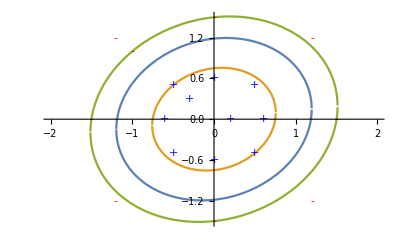

```mathematica
bound[x1_] = x2/.NSolve[{Simplify[f[{x1,x2}]]==0},{x2}];
bound1[x1_] = x2/.Solve[{Simplify[f[{x1,x2}]]==1},{x2}];
bound2[x1_] = x2/.Solve[{Simplify[f[{x1,x2}]]==-1},{x2}];

picbound = Plot[{bound[x1],bound1[x1],bound2[x1]},{x1,-2,2}];

Print[Show[{picbound,picpts}]];
```

```mathematica
f2[{x1_,x2_}] = Expand[Simplify[f[{x1,x2}]]];
f3[x_] := If[f2[x]<0,-1,1];

l = {#[[1]],#[[2]],f2[#[[1]]],f3[#[[1]]],f3[#[[1]]]-#[[2]],Abs[#[[2]]-f2[#[[1]]]]}&/@Transpose[{xs,ys}];
l2 = Select[l,#[[5]]!=0&];
l3 = Select[l,Abs[#[[3]]]<0.9999&];

Print["Misclassified (and uses slack): ",MatrixForm[If[l2=={},{},Prepend[l2,{"x^-","y","f2[x^-]","f[x^-]","f[x^-]-y","ξ"}]]]];
Print["Not misclassified but uses slack: ",MatrixForm[Prepend[l3,{"x^-","y","f2[x^-]","f[x^-]","f[x^-]-y","ξ"}]]];
```

Misclassified (and uses slack): {}

Not misclassified but uses slack: (x^- | y | f2[x^-] | f[x^-] | f[x^-]-y | ξ)

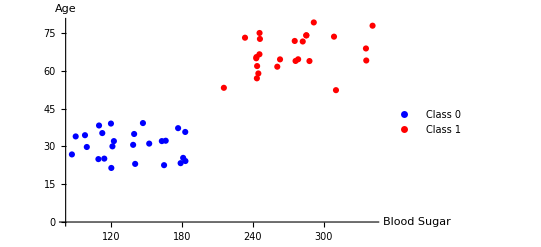

Training Set = (x_1 | x_2 | y
178.914 | 23.3724 | 0
164.899 | 22.5733 | 0
138.716 | 30.6445 | 0
97.965 | 34.4738 | 0
163.017 | 32.1334 | 0
182.982 | 24.2162 | 0
181.054 | 25.4691 | 0
182.824 | 35.7612 | 0
140.434 | 23.0759 | 0
99.5096 | 29.7931 | 0
114.294 | 25.173 | 0
86.8959 | 26.8393 | 0
122.429 | 32.1268 | 0
139.563 | 34.9546 | 0
90.0949 | 33.9873 | 0
112.605 | 35.3168 | 0
176.777 | 37.271 | 0
120.253 | 21.4658 | 0
109.851 | 38.3296 | 0
109.322 | 24.9824 | 0
166.291 | 32.2807 | 0
147.012 | 39.2915 | 0
121.203 | 30.0405 | 0
152.318 | 31.1375 | 0
119.943 | 39.0979 | 0
260.732 | 61.6763 | 1
245.638 | 66.6156 | 1
278.394 | 64.6212 | 1
287.965 | 63.9244 | 1
246.043 | 72.7066 | 1
335.78 | 68.9168 | 1
263.054 | 64.5855 | 1
282.284 | 71.6923 | 1
341.38 | 77.9603 | 1
243.662 | 61.9257 | 1
215.516 | 53.2958 | 1
243.463 | 57.0609 | 1
233.413 | 73.1925 | 1
291.633 | 79.254 | 1
275.494 | 71.8974 | 1
310.406 | 52.3603 | 1
308.741 | 73.6065 | 1
285.349 | 74.1499 | 1
243.116 | 65.5121 | 1
245.721 | 75.0638 | 1
336.054 | 64.1431 | 1
242.889 | 65.0228 | 1
276.2 | 63.9573 | 1
244.709 | 58.9937 | 1
285.265 | 74.1009 | 1)  →  (i | (x^-)_i | y_i | α_i
1 | {178.914,23.3724} | 0 | α[1]
2 | {164.899,22.5733} | 0 | α[2]
3 | {138.716,30.6445} | 0 | α[3]
4 | {97.965,34.4738} | 0 | α[4]
5 | {163.017,32.1334} | 0 | α[5]
6 | {182.982,24.2162} | 0 | α[6]
7 | {181.054,25.4691} | 0 | α[7]
8 | {182.824,35.7612} | 0 | α[8]
9 | {140.434,23.0759} | 0 | α[9]
10 | {99.5096,29.7931} | 0 | α[10]
11 | {114.294,25.173} | 0 | α[11]
12 | {86.8959,26.8393} | 0 | α[12]
13 | {122.429,32.1268} | 0 | α[13]
14 | {139.563,34.9546} | 0 | α[14]
15 | {90.0949,33.9873} | 0 | α[15]
16 | {112.605,35.3168} | 0 | α[16]
17 | {176.777,37.271} | 0 | α[17]
18 | {120.253,21.4658} | 0 | α[18]
19 | {109.851,38.3296} | 0 | α[19]
20 | {109.322,24.9824} | 0 | α[20]
21 | {166.291,32.2807} | 0 | α[21]
22 | {147.012,39.2915} | 0 | α[22]
23 | {121.203,30.0405} | 0 | α[23]
24 | {152.318,31.1375} | 0 | α[24]
25 | {119.943,39.0979} | 0 | α[25]
26 | {260.732,61.6763} | 1 | α[26]
27 | {245.638,66.6156} | 1 | α[27]
28 | {278.394,64.6212} | 1 | α[28]
29 | {287.965,63.9244} | 1 | α[29]
30 | {246.043,72.7066} | 1 | α[30]
31 | {335.78,68.9168} | 1 | α[31]
32 | {263.054,64.5855} | 1 | α[32]
33 | {282.284,71.6923} | 1 | α[33]
34 | {341.38,77.9603} | 1 | α[34]
35 | {243.662,61.9257} | 1 | α[35]
36 | {215.516,53.2958} | 1 | α[36]
37 | {243.463,57.0609} | 1 | α[37]
38 | {233.413,73.1925} | 1 | α[38]
39 | {291.633,79.254} | 1 | α[39]
40 | {275.494,71.8974} | 1 | α[40]
41 | {310.406,52.3603} | 1 | α[41]
42 | {308.741,73.6065} | 1 | α[42]
43 | {285.349,74.1499} | 1 | α[43]
44 | {243.116,65.5121} | 1 | α[44]
45 | {245.721,75.0638} | 1 | α[45]
46 | {336.054,64.1431} | 1 | α[46]
47 | {242.889,65.0228} | 1 | α[47]
48 | {276.2,63.9573} | 1 | α[48]
49 | {244.709,58.9937} | 1 | α[49]
50 | {285.265,74.1009} | 1 | α[50])

```mathematica
(*Attempt 2*)
Clear[trainingSetOriginal,len,αs,trainingSet,x,y]

(*Generate linearly separable dataset*)
diabetesData=Table[{RandomReal[{80,190}],RandomReal[{20,40}],0},{i,1,25}];
diabetesData=Join[diabetesData,Table[{RandomReal[{210,350}],RandomReal[{50,80}],1},{i,1,25}]];

ListPlot[{Cases[diabetesData,{x_,y_,0}->{x,y}],Cases[diabetesData,{x_,y_,1}->{x,y}]},PlotStyle->{Blue,Red},AxesLabel->{"Blood Sugar","Age"},PlotLegends->{"Class 0","Class 1"}]

trainingSetOriginal=diabetesData;

len = Length[trainingSetOriginal];
αs = Table[α[i] ,{i,1,len}];


trainingSet = Map[{{#[[1]],#[[2]]},#[[3]]}&,trainingSetOriginal];
trainingSet = Transpose[trainingSet];
{x,y} = trainingSet;
PrependTo[trainingSet,Range[len]];
AppendTo[trainingSet,αs];
trainingSet = Transpose[trainingSet];

Print["Training Set = ",MatrixForm[Prepend[trainingSetOriginal,{"x_1","x_2","y"}]],"  →  ",MatrixForm[Prepend[trainingSet,{"i","(x^-)_i","y_i","α_i"}]],""];
```

```mathematica
i=50;
x[[i]]
y[[i]]
αs[[i]]
```

{233.256,60.5669}

1

α[50]

```mathematica
Total[αs]
```

α[1]+α[2]+α[3]+α[4]+α[5]+α[6]+α[7]+α[8]+α[9]+α[10]+α[11]+α[12]+α[13]+α[14]+α[15]+α[16]+α[17]+α[18]+α[19]+α[20]+α[21]+α[22]+α[23]+α[24]+α[25]+α[26]+α[27]+α[28]+α[29]+α[30]+α[31]+α[32]+α[33]+α[34]+α[35]+α[36]+α[37]+α[38]+α[39]+α[40]+α[41]+α[42]+α[43]+α[44]+α[45]+α[46]+α[47]+α[48]+α[49]+α[50]

```mathematica
ClearAll[lag,constraints,maxval,αNum,αNumRounded,αValues,wDual,bDual,svLabels];

lag = Total[Table[       α[i]         ,{i,1,len}]]-1/2 Total[Flatten[Table[        α[i] α[j] y[[i]] y[[j]] x[[i]].x[[j]]            ,{i,1,len},{j,1,len}]]];
constraints=Table[α[i]≥0,{i,1,len}];
constraints[[1]]=Total[Table[α[i] y[[i]],{i,1,len}]]==0;

{maxval,αNum}=NMaximize[{lag,constraints},Table[α[i],{i,1,len}]];


{maxval,αNum} = NMaximize[{lag,constraints},Table[α[i],{i,1,len}]];                                                 (* this is the important line of code! *)


αNumRounded = Round[10^3 (Table[α[i] ,{i,1,len}]/.αNum)] 1.0 10^-3;
svLabels = Complement[Range[len],Flatten[Position[αNumRounded,0.0]]];

αValues = Table[α[i] ,{i,1,len}] /.αNum;
wDual = Total[αValues y x];

sv1 = svLabels[[1]];
bDual = y[[sv1]]- wDual.x[[sv1]];






Print["For this problem we have the following DUAL PROBLEM"];
Print["Maximize Q(α) = ",lag];
Print["Subject to the following constraints: ",MatrixForm[constraints]];
Print["The Numerical Analysis Programme comes back with the following information:

Max found: ",maxval, " αs found: ",MatrixForm[αNum]," i.e. ",MatrixForm[Table[Subscript[α,i] ,{i,1,len}]],"=",MatrixForm[Round[10^3 (Table[α[i] ,{i,1,len}]/.αNum)] 1.0 10^-3 ]," to 3 d.p."];


Print["As a result we find the non-zero α_is have labels: ",svLabels];

Print["Using the α_is we can then find w and b:"];
Print["w^- = Σ α_i y_i (x^-)_i = ",
Total[Times@@{Subscript["α",#],Subscript[" y",#],Subscript[" x",#]}&/@svLabels]," = ",MatrixForm[wDual]];

Print["Since ",Subscript["α",sv1]," is non-zero 
we can find  b = y[[",sv1,"]] - w^-. x[[",sv1,"]] = ",y[[sv1]]," - ",MatrixForm[wDual],".",MatrixForm[x[[sv1]]]," = ",bDual];
```

NMaximize::dinfeas: The dual is infeasible, which implies that the primal optimization is either unbounded or infeasible.

For this problem we have the following DUAL PROBLEM

Maximize Q(α) = α[1]+α[2]+α[3]+α[4]+α[5]+α[6]+α[7]+α[8]+α[9]+α[10]+α[11]+α[12]+α[13]+α[14]+α[15]+α[16]+α[17]+α[18]+α[19]+α[20]+α[21]+α[22]+α[23]+α[24]+α[25]+α[26]+α[27]+α[28]+α[29]+α[30]+α[31]+α[32]+α[33]+α[34]+α[35]+α[36]+α[37]+α[38]+α[39]+α[40]+α[41]+α[42]+α[43]+α[44]+α[45]+α[46]+α[47]+α[48]+α[49]+α[50]+1/2 (0.-71785. α[26]^2-136309. α[26] α[27]-64775.8 α[27]^2-153144. α[26] α[28]-145378. α[27] α[28]-81679.4 α[28]^2-158048. α[26] α[29]-149987. α[27] α[29]-168597. α[28] α[29]-87010. α[29]^2-137271. α[26] α[30]-130562. α[27] α[30]-146391. α[28] α[30]-150999. α[29] α[30]-65823.2 α[30]^2-183598. α[26] α[31]-174143. α[27] α[31]-195865. α[28] α[31]-202196. α[29] α[31]-175254. α[30] α[31]-117497. α[31]^2-145140. α[26] α[32]-137837. α[27] α[32]-154813. α[28] α[32]-159758. α[29] α[32]-138837. α[30] α[32]-185559. α[31] α[32]-73368.8 α[32]^2-156044. α[26] α[33]-148231. α[27] α[33]-166438. α[28] α[33]-171741. α[29] α[33]-149333. α[30] α[33]-199452. α[31] α[33]-157773. α[32] α[33]-84824. α[33]^2-187634. α[26] α[34]-178099. α[27] α[34]-200152. α[28] α[34]-206578. α[29] α[34]-179324. α[30] α[34]-240002. α[31] α[34]-189673. α[32] α[34]-203910. α[33] α[34]-122618. α[34]^2-134700. α[26] α[35]-127956. α[27] α[35]-143672. α[28] α[35]-148249. α[29] α[35]-128907. α[30] α[35]-172169. α[31] α[35]-136192. α[32] α[35]-146443. α[33] α[35]-176018. α[34] α[35]-63206.1 α[35]^2-118958. α[26] α[36]-112979. α[27] α[36]-126885. α[28] α[36]-130936. α[29] α[36]-113802. α[30] α[36]-152078. α[31] α[36]-120269. α[32] α[36]-129315. α[33] α[36]-155456. α[34] α[36]-111627. α[35] α[36]-49287.8 α[36]^2-133996. α[26] α[37]-127210. α[27] α[37]-142932. α[28] α[37]-147513. α[29] α[37]-128102. α[30] α[37]-171365. α[31] α[37]-135459. α[32] α[37]-145633. α[33] α[37]-175124. α[34] α[37]-125713. α[35] α[37]-111023. α[36] α[37]-62530.3 α[37]^2-130745. α[26] α[38]-124422. α[27] α[38]-139421. α[28] α[38]-143787. α[29] α[38]-125502. α[30] α[38]-166839. α[31] α[38]-132255. α[32] α[38]-142272. α[33] α[38]-170777. α[34] α[38]-122813. α[35] α[38]-108410. α[36] α[38]-122008. α[37] α[38]-59838.6 α[38]^2-161852. α[26] α[39]-153832. α[27] α[39]-172621. α[28] α[39]-178093. α[29] α[39]-155033. α[30] α[39]-206773. α[31] α[39]-163668. α[32] α[39]-176010. α[33] α[39]-211472. α[34] α[39]-151936. α[35] α[39]-134151. α[36] α[39]-151048. α[37] α[39]-147743. α[38] α[39]-91330.9 α[39]^2-152529. α[26] α[40]-144923. α[27] α[40]-162684. α[28] α[40]-167857. α[29] α[40]-146022. α[30] α[40]-194921. α[31] α[40]-154227. α[32] α[40]-165844. α[33] α[40]-199307. α[34] α[40]-143160. α[35] α[40]-126411. α[36] α[40]-142351. α[37] α[40]-139132. α[38] α[40]-172083. α[39] α[40]-81066.4 α[40]^2-168324. α[26] α[41]-159471. α[27] α[41]-179598. α[28] α[41]-185466. α[29] α[41]-160360. α[30] α[41]-215673. α[31] α[41]-170071. α[32] α[41]-182753. α[33] α[41]-220097. α[34] α[41]-157753. α[35] α[41]-139376. α[36] α[41]-157120. α[37] α[41]-152570. α[38] α[41]-189349. α[39] α[41]-178559. α[40] α[41]-99093.4 α[41]^2-170077. α[26] α[42]-161484. α[27] α[42]-181417. α[28] α[42]-187224. α[29] α[42]-162630. α[30] α[42]-217483. α[31] α[42]-171939. α[32] α[42]-184859. α[33] α[42]-222272. α[34] α[42]-159573. α[35] α[42]-140923. α[36] α[42]-158734. α[37] α[42]-154903. α[38] α[42]-191745. α[39] α[42]-180697. α[40] α[42]-199378. α[41] α[42]-100739. α[42]^2-157946. α[26] α[43]-150064. α[27] α[43]-168462. α[28] α[43]-173821. α[29] α[43]-151198. α[30] α[43]-201849. α[31] α[43]-159703. α[32] α[43]-171731. α[33] α[43]-206386. α[34] α[43]-148241. α[35] α[43]-130899. α[36] α[43]-147406. α[37] α[43]-144062. α[38] α[43]-178188. α[39] α[43]-167886. α[40] α[43]-184913. α[41] α[43]-187114. α[42] α[43]-86922.2 α[43]^2-134857. α[26] α[44]-128166. α[27] α[44]-143831. α[28] α[44]-148393. α[29] α[44]-129160. α[30] α[44]-172297. α[31] α[44]-136368. α[32] α[44]-146649. α[33] α[44]-176204. α[34] α[44]-126590. α[35] α[44]-111774. α[36] α[44]-125856. α[37] α[44]-123083. α[38] α[44]-152186. α[39] α[44]-143375. α[40] α[44]-157790. α[41] α[44]-159764. α[42] α[44]-148461. α[43] α[44]-63397.3 α[44]^2-137394. α[26] α[45]-130718. α[27] α[45]-146516. α[28] α[45]-151115. α[29] α[45]-131831. α[30] α[45]-175363. α[31] α[45]-138972. α[32] α[45]-149489. α[33] α[45]-179472. α[34] α[45]-129043. α[35] α[45]-113915. α[36] α[45]-128215. α[37] α[45]-125697. α[38] α[45]-155219. α[39] α[45]-146183. α[40] α[45]-160407. α[41] α[45]-162779. α[42] α[45]-151364. α[43] α[45]-129313. α[44] α[45]-66013.4 α[45]^2-183152. α[26] α[46]-173641. α[27] α[46]-195401. α[28] α[46]-201744. α[29] α[46]-174695. α[30] α[46]-234521. α[31] α[46]-185086. α[32] α[46]-198923. α[33] α[46]-239445. α[34] α[46]-171712. α[35] α[46]-151687. α[36] α[46]-170954. α[37] α[46]-166268. α[38] α[46]-206176. α[39] α[46]-194385. α[40] α[46]-215343. α[41] α[46]-216950. α[42] α[46]-201298. α[43] α[46]-171805. α[44] α[46]-174781. α[45] α[46]-117047. α[46]^2-134678. α[26] α[47]-127989. α[27] α[47]-143641. α[28] α[47]-148200. α[29] α[47]-128977. α[30] α[47]-172076. α[31] α[47]-136185. α[32] α[47]-146450. α[33] α[47]-175973. α[34] α[47]-126419. α[35] α[47]-111624. α[36] α[47]-125690. α[37] α[47]-122905. α[38] α[47]-151975. α[39] α[47]-143179. α[40] α[47]-157597. α[41] α[47]-159552. α[42] α[47]-148259. α[43] α[47]-126620. α[44] α[47]-129127. α[45] α[47]-171589. α[46] α[47]-63222.9 α[47]^2-151918. α[26] α[48]-144212. α[27] α[48]-162051. α[28] α[48]-167249. α[29] α[48]-145214. α[30] α[48]-194300. α[31] α[48]-153573. α[32] α[48]-165104. α[33] α[48]-198551. α[34] α[48]-142520. α[35] α[48]-125869. α[36] α[48]-141788. α[37] α[48]-138300. α[38] α[48]-171236. α[39] α[48]-161380. α[40] α[48]-178166. α[41] α[48]-179964. α[42] α[48]-167112. α[43] α[48]-142678. α[44] α[48]-145338. α[45] α[48]-193841. α[46] α[48]-142489. α[47] α[48]-80377.2 α[48]^2-134884. α[26] α[49]-128079. α[27] α[49]-143876. α[28] α[49]-148477. α[29] α[49]-128996. α[30] α[49]-172468. α[31] α[49]-136364. α[32] α[49]-146613. α[33] α[49]-176275. α[34] α[49]-126559. α[35] α[49]-111766. α[36] α[49]-125888. α[37] α[49]-122872. α[38] α[49]-152081. α[39] α[49]-143315. α[40] α[49]-158096. α[41] α[49]-159788. α[42] α[49]-148403. α[43] α[49]-126715. α[44] α[49]-129117. α[45] α[49]-172039. α[46] α[49]-126546. α[47] α[49]-142723. α[48] α[49]-63362.6 α[49]^2-157896. α[26] α[50]-150016. α[27] α[50]-168409. α[28] α[50]-173766. α[29] α[50]-151150. α[30] α[50]-201786. α[31] α[50]-159652. α[32] α[50]-171676. α[33] α[50]-206321. α[34] α[50]-148194. α[35] α[50]-130857. α[36] α[50]-147359. α[37] α[50]-144016. α[38] α[50]-178131. α[39] α[50]-167833. α[40] α[50]-184856. α[41] α[50]-187054. α[42] α[50]-173789. α[43] α[50]-148414. α[44] α[50]-151316. α[45] α[50]-201235. α[46] α[50]-148212. α[47] α[50]-167059. α[48] α[50]-148356. α[49] α[50]-86866.8 α[50]^2)

Subject to the following constraints: (α[26]+α[27]+α[28]+α[29]+α[30]+α[31]+α[32]+α[33]+α[34]+α[35]+α[36]+α[37]+α[38]+α[39]+α[40]+α[41]+α[42]+α[43]+α[44]+α[45]+α[46]+α[47]+α[48]+α[49]+α[50]==0
α[2]≥0
α[3]≥0
α[4]≥0
α[5]≥0
α[6]≥0
α[7]≥0
α[8]≥0
α[9]≥0
α[10]≥0
α[11]≥0
α[12]≥0
α[13]≥0
α[14]≥0
α[15]≥0
α[16]≥0
α[17]≥0
α[18]≥0
α[19]≥0
α[20]≥0
α[21]≥0
α[22]≥0
α[23]≥0
α[24]≥0
α[25]≥0
α[26]≥0
α[27]≥0
α[28]≥0
α[29]≥0
α[30]≥0
α[31]≥0
α[32]≥0
α[33]≥0
α[34]≥0
α[35]≥0
α[36]≥0
α[37]≥0
α[38]≥0
α[39]≥0
α[40]≥0
α[41]≥0
α[42]≥0
α[43]≥0
α[44]≥0
α[45]≥0
α[46]≥0
α[47]≥0
α[48]≥0
α[49]≥0
α[50]≥0)

The Numerical Analysis Programme comes back with the following information:

Max found: ∞ αs found: (α[1]→Indeterminate
α[2]→Indeterminate
α[3]→Indeterminate
α[4]→Indeterminate
α[5]→Indeterminate
α[6]→Indeterminate
α[7]→Indeterminate
α[8]→Indeterminate
α[9]→Indeterminate
α[10]→Indeterminate
α[11]→Indeterminate
α[12]→Indeterminate
α[13]→Indeterminate
α[14]→Indeterminate
α[15]→Indeterminate
α[16]→Indeterminate
α[17]→Indeterminate
α[18]→Indeterminate
α[19]→Indeterminate
α[20]→Indeterminate
α[21]→Indeterminate
α[22]→Indeterminate
α[23]→Indeterminate
α[24]→Indeterminate
α[25]→Indeterminate
α[26]→Indeterminate
α[27]→Indeterminate
α[28]→Indeterminate
α[29]→Indeterminate
α[30]→Indeterminate
α[31]→Indeterminate
α[32]→Indeterminate
α[33]→Indeterminate
α[34]→Indeterminate
α[35]→Indeterminate
α[36]→Indeterminate
α[37]→Indeterminate
α[38]→Indeterminate
α[39]→Indeterminate
α[40]→Indeterminate
α[41]→Indeterminate
α[42]→Indeterminate
α[43]→Indeterminate
α[44]→Indeterminate
α[45]→Indeterminate
α[46]→Indeterminate
α[47]→Indeterminate
α[48]→Indeterminate
α[49]→Indeterminate
α[50]→Indeterminate) i.e. (α_1
α_2
α_3
α_4
α_5
α_6
α_7
α_8
α_9
α_10
α_11
α_12
α_13
α_14
α_15
α_16
α_17
α_18
α_19
α_20
α_21
α_22
α_23
α_24
α_25
α_26
α_27
α_28
α_29
α_30
α_31
α_32
α_33
α_34
α_35
α_36
α_37
α_38
α_39
α_40
α_41
α_42
α_43
α_44
α_45
α_46
α_47
α_48
α_49
α_50)=(Indeterminate
Indeterminate
Indeterminate
Indeterminate
Indeterminate
Indeterminate
Indeterminate
Indeterminate
Indeterminate
Indeterminate
Indeterminate
Indeterminate
Indeterminate
Indeterminate
Indeterminate
Indeterminate
Indeterminate
Indeterminate
Indeterminate
Indeterminate
Indeterminate
Indeterminate
Indeterminate
Indeterminate
Indeterminate
Indeterminate
Indeterminate
Indeterminate
Indeterminate
Indeterminate
Indeterminate
Indeterminate
Indeterminate
Indeterminate
Indeterminate
Indeterminate
Indeterminate
Indeterminate
Indeterminate
Indeterminate
Indeterminate
Indeterminate
Indeterminate
Indeterminate
Indeterminate
Indeterminate
Indeterminate
Indeterminate
Indeterminate
Indeterminate) to 3 d.p.

As a result we find the non-zero α_is have labels: {1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50}

Using the α_is we can then find w and b:

w^- = Σ α_i y_i (x^-)_i = x_1 y_1 α_1+x_2 y_2 α_2+x_3 y_3 α_3+x_4 y_4 α_4+x_5 y_5 α_5+x_6 y_6 α_6+x_7 y_7 α_7+x_8 y_8 α_8+x_9 y_9 α_9+x_10 y_10 α_10+x_11 y_11 α_11+x_12 y_12 α_12+x_13 y_13 α_13+x_14 y_14 α_14+x_15 y_15 α_15+x_16 y_16 α_16+x_17 y_17 α_17+x_18 y_18 α_18+x_19 y_19 α_19+x_20 y_20 α_20+x_21 y_21 α_21+x_22 y_22 α_22+x_23 y_23 α_23+x_24 y_24 α_24+x_25 y_25 α_25+x_26 y_26 α_26+x_27 y_27 α_27+x_28 y_28 α_28+x_29 y_29 α_29+x_30 y_30 α_30+x_31 y_31 α_31+x_32 y_32 α_32+x_33 y_33 α_33+x_34 y_34 α_34+x_35 y_35 α_35+x_36 y_36 α_36+x_37 y_37 α_37+x_38 y_38 α_38+x_39 y_39 α_39+x_40 y_40 α_40+x_41 y_41 α_41+x_42 y_42 α_42+x_43 y_43 α_43+x_44 y_44 α_44+x_45 y_45 α_45+x_46 y_46 α_46+x_47 y_47 α_47+x_48 y_48 α_48+x_49 y_49 α_49+x_50 y_50 α_50 = (Indeterminate
Indeterminate)

Since α_1 is non-zero 
we can find  b = y[[1]] - w^-. x[[1]] = 0 - (Indeterminate
Indeterminate).(178.914
23.3724) = Indeterminate